## Pendulum swing up & balance, with local linear feedback (Example 7.7)

```mathematica
Clear["Global`*"];

ffCalc[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff0,θdotff0,uff0,θff,θdotff,uff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}] := {θdot,-Sin[θ]-λ,λdot,-Cos[θ]λ};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}== {Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}
+Δt/2(f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ}];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];

θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{θff,θdotff,uff}]

n=500;  τ=5;τ1=3τ;
{θ0,θdot0,u0}=ffCalc[n,τ];
p0=Plot[{θ0[t],u0[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-1,4}];
```

Test the approximate solution on the open-loop dynamics (integrated at a fine time step)

```mathematica
TestSwingUp[τ1_,uff_]:=Module[{eq,init,θ,θdot,θs,θdots,us,t},
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+uff[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}]//Quiet;
θs]

θ1=TestSwingUp[τ1,u0];
p1=Plot[{θ1[t],u0[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
```

Show that linear feedback can stabilize against various perturbations

```mathematica
TestSwingUpFB[τ_,τ1_,d_,θff_,θdotff_,uff_]:=Module[{eq,init,θ,θdot,t,κ1,κ2,ufb,u,td1,td2,td3},
κ1=κ2=√2+1;  (* lqr for q=r for balancing pendulum *)
td1=3;td2=8;td3=13;
ufb[t_]:=Piecewise[{{κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t]),0≤t≤td3-0.1}},0];

eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+u[t],u[t]==uff[t]+ufb[t]};
init={θ[0]==θdot[0]==0};

NDSolveValue[{eq,init,WhenEvent[{t==td1,t==td2,t==td3},θdot[t]-> θdot[t]-d]},{θ,θdot,u},{t,0,τ1}]//Quiet]

d=0.7;
{θ2,θdot2,u2}=TestSwingUpFB[τ,τ1,d,θ0,θdot0,u0];
p2=Plot[{θ2[t],u2[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4},Filling->{2->Axis}];
```

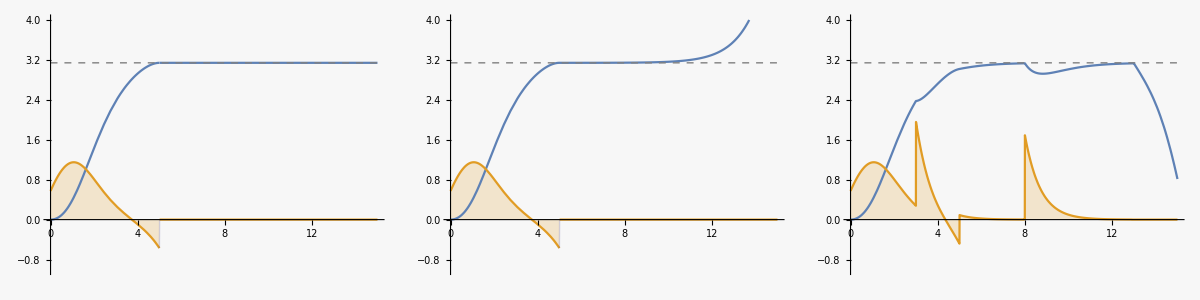

```mathematica
Grid[{{p0,p1,p2}},Spacings->4]
```

Export data

```mathematica
dt=0.05;
dat=Table[Through[{θ0,u0,θ1,θ2,u2}[t]],{t,0,τ1,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumPert.dat", dat] 
*)
```